A plot of a rotated ellipse showing the major and minor axes, and the angle of rotation.  This was related to an elliptically polarized plane wave.

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16];
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

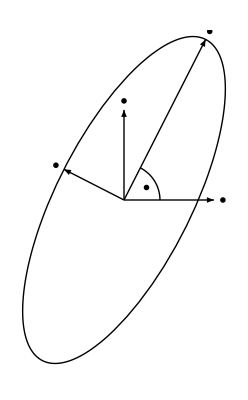

```mathematica
ClearAll[ellipticalPolarizationFig1, bold, boldsubx, subx, te, ellipse]

bold = MaTeX[ "\\mathbf{"<>#<>"}"] &;
boldsubx[x_, i_, s_ : "_"] := (MaTeX[ "\\mathbf{" <> x <>"}" <>s <> i] ) ;
subx[x_, i_, s_ : "_"] := (MaTeX[ x <>"" <>s <> i] ) ;
te[n_] := boldsubx["e", ToString[n]];

ellipse[a_, b_, psi_,phi_] := Module[{e,mu,f},
e = Sqrt[1 - (b/a)^2];
mu = ArcTanh[ b/a ];
f = e a Exp[I psi] Cosh[ mu + I phi] ;
{f//Re,f//Im}
]



plotEllipse[a_, b_, psi_] :=Module[{te1, te2, e1, e2, o, va, vb, ea,eb,s},
o = {0,0};
va = ellipse[a,b,psi,0];
vb = ellipse[a,b,psi,Pi/2];
s = 0.1;
{e1,e2} = IdentityMatrix[2];
te1 = boldsubx["e", "1"];
te2 = boldsubx["e", "2"];
ea = boldsubx["E", "a"];
eb = boldsubx["E", "b"];
Show[{
ParametricPlot[
ellipse[a,b,psi, t],{t,0,2 Pi},
Ticks  -> None,
PlotStyle-> {Thick, Black},
Axes -> None
],
ParametricPlot[(a/5){Cos[t],Sin[t]},{t,0,psi}, PlotStyle->{ Thick,Black}],
Graphics[{
Thick,
Arrow[{o, e1}],
Arrow[{o, e2}],
Text[te1, (1+s) e1],
Text[te2, (1+s) e2],
Arrow[{o,va}],
Arrow[{o,vb}],
Text[ea, va + s(va//Normalize)],
Text[eb, vb + s(vb//Normalize)],
Text[ "\\phi"//MaTeX, ellipse[a,b,psi/2,0]/7]
}
,AspectRatio-> 1
]
}]
];

ellipticalPolarizationFig1 = plotEllipse[2,.75,0.35 Pi] 
(*p2 = plotEllipse[3,0,0.35 Pi] *)
```

```mathematica
peeters`exportForLatex["ellipticalPolarizationFig1", ellipticalPolarizationFig1]
```

{ellipticalPolarizationFig1.eps,ellipticalPolarizationFig1pn.png}

```mathematica
Manipulate[
plotEllipse[a,b,psi] 
,{{a,3, "E_a"},1,100}
,{{b,1.5, "E_b"},0,0.99 a}
, {{psi,0.35 Pi, "ψ"},0, 2Pi}
]
```